```mathematica
(*
Subscript[χ, inc] = Cos[π/4];
RI = KerrGeoISSO[a,Subscript[χ, inc]];
L = KerrGeoAngularMomentum[a,KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ];
Q = KerrGeoCarterConstant[a,KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ];
ϵ =KerrGeoEnergy[a, KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ];*)
```

```mathematica
(*Subscript[χ, inc] = Cos[π/4.37];
M=1
a = 0.689;

RI= KerrGeoISSO[a,Subscript[χ, inc]];
RM = M- Sqrt[M^2-a^2];
RP = M+ Sqrt[M^2-a^2];

Q=-M(RI)^(5/2)((Sqrt[(RI-RP)(RI-RM)]-2Sqrt[RI])^2-4 a^2)/(4 a^2(RI^(3/2)-Sqrt[RI]-Sqrt[(RI-RP)(RI-RM)]))
Qbh = KerrGeoCarterConstant[a,KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ]
ϵ =(√(a^2 Q-2 M RI^3+3 RI^4))/(√3 RI^2)
ϵbh =KerrGeoEnergy[a, KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ]


L1=(√(3 a^2 Q-a^2 RI^2-Q RI^2+3 RI^4+a^2 RI^2 ϵ^2-3 RI^4 ϵ^2))/RI

Lbh= KerrGeoAngularMomentum[a,KerrGeoISSO[a,ang ],0,ang  ]

Plot[{Re[L1[R]],Im[L1[R]]},{R,0,30}];
Plot[{Re[Q[R]],Im[Q[R]]},{R,0,30}];
Plot[{Re[ϵ[R]],Im[ϵ[R]]},{R,0,30}];
```

## Setting Up Equations

```mathematica
Clear["Global`*"]
```

## Solving for RISSOMIN and RISSOPLUS

## Range check for possible ISSO’s

{3.39313,8.14297}

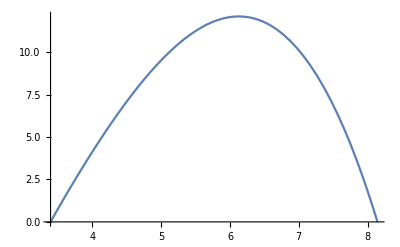

```mathematica
a = 0.7;
M = 1;
RM = M- Sqrt[M^2-a^2];
RP = M+ Sqrt[M^2-a^2];
DN = (27-45 a^2+17 a^4+a^6+8 a^3 (1-a^2))^(1/3);
{RISSOMIN,RISSOMAX  }={ 3+√(3+a^2+(9-10 a^2+a^4)/DN+DN)-1/2 √(72+8 (-6+a^2)-(4 (9-10 a^2+a^4))/DN-4 DN+(64 a^2)/(√(3+a^2+(9-10 a^2+a^4)/DN+DN))),3+√(3+a^2+(9-10 a^2+a^4)/DN+DN)+1/2 √(72+8 (-6+a^2)-(4 (9-10 a^2+a^4))/DN-4 DN+(64 a^2)/(√(3+a^2+(9-10 a^2+a^4)/DN+DN)))}


Plot[Re[- M(RI)^(5/2)((Sqrt[(RI-RP)(RI-RM)]-2Sqrt[RI])^2-4 a^2)/(4 a^2(RI^(3/2)-Sqrt[RI]-Sqrt[(RI-RP)(RI-RM)]))],{RI,RISSOMIN,RISSOMAX}]
```

```mathematica
ClearAll;
(*Subscript[χ, inc] = Cos[π/4.37];*)
(*RI= KerrGeoISSO[a,Subscript[χ, inc]];*)
(*Gam = RI^5-Q(RI-3)RI^3+a^2 Q^2;

ϵ= (RI^3(RI-2)-a(a Q+Sqrt[Gam ]))/(RI^2 Sqrt[RI^3(RI-3)-2a(a Q+Sqrt[Gam ])])*)
(*L =- (2 a RI^3+(RI^2+a^2)(a Q +Sqrt[Gam]))/(RI^2 Sqrt[RI^3(RI-3)-2a(a Q+Sqrt[Gam ])])*)
 (*Sqrt[(-a^2-L^2-Q+a^2 ϵ^2-√(12 a^2 Q (-3+3 ϵ^2)+(a^2+L^2+Q-a^2 ϵ^2)^2))/(6 (-1+ϵ^2))]*)


RI=7.5;
Q =- M(RI)^(5/2)((Sqrt[(RI-RP)(RI-RM)]-2Sqrt[RI])^2-4 a^2)/(4 a^2(RI^(3/2)-Sqrt[RI]-Sqrt[(RI-RP)(RI-RM)]))
ϵ=(√(a^2 Q-2 RI^3+3 RI^4))/(√3 RI^2)
LMPBOUND = Nearest[x/.NSolve[Sqrt[-a^2 x^2+2 x^3+(a^2 (-2 x^3+3 x^4-(M x^(5/2) (-4 a^2+(-2 Sqrt[x]+Sqrt[(x-RM) (x-RP)])^2))/(4 (-Sqrt[x]+x^(3/2)-Sqrt[(x-RM) (x-RP)]))))/(3 x^2)-(M x^(5/2) (-4 a^2+(-2 Sqrt[x]+Sqrt[(x-RM) (x-RP)])^2))/(2 (-Sqrt[x]+x^(3/2)-Sqrt[(x-RM) (x-RP)]))+(M x^(9/2) (-4 a^2+(-2 Sqrt[x]+Sqrt[(x-RM) (x-RP)])^2))/(4 a^2 (-Sqrt[x]+x^(3/2)-Sqrt[(x-RM) (x-RP)]))]/x==0,x],6][[1]];
	If[Element[LMPBOUND ,Complexes], LMPBOUND=6];
L=Piecewise[{{Sqrt[3 a^2 Q-a^2 RI^2-Q RI^2+3 RI^4+a^2 RI^2 ϵ^2-3 RI^4 ϵ^2]/RI,RI< LMPBOUND},{Sqrt[3 a^2 Q-a^2 RI^2-Q RI^2+3 RI^4+a^2 RI^2 ϵ^2-3 RI^4 ϵ^2]/-RI, LMPBOUND<=RI}}];
	
J = 1-ϵ^2;
R4 =(a^2 Q)/(J*RI^3) ;
Z1=Sqrt[1/2 (1+(L^2+Q)/(a^2 (1-ϵ^2))-√(-(4 Q)/(a^2 (1-ϵ^2))+(-1-(L^2+Q)/(a^2 (1-ϵ^2)))^2))];
Z2 =Sqrt[ (a^2(1-ϵ^2))/2 (1+(L^2+Q)/(a^2 (1-ϵ^2))+√(-(4 Q)/(a^2 (1-ϵ^2))+(-1-(L^2+Q)/(a^2 (1-ϵ^2)))^2))];
KZ = a^2*J(Z1^2/Z2^2);
```

6.88123

0.954707

```mathematica
R0 = (RI+RP)/2
```

4.60707

### λ of R equation

```mathematica
Mino[r_]:=(2 √(r-R4))/(√(J (RI-r) (R4-RI)^2));
(*Solve[-3 R+3 R ϵ^2-(3 a^2 Q)/(R (1-ϵ^2))+(3 a^2 Q ϵ^2)/(R (1-ϵ^2))==-a^2-Q+4 a ϵ+2 a^2 ϵ^2-(2+a ϵ)^2,R];*)
```

### Radial Equation

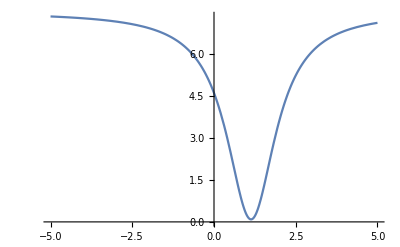

```mathematica
r[λ_]:=((RI(RI-R4)^2 J*(λ-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))^2+4*R4)/((RI-R4)^2 J*(λ-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))^2+4));
Plot[r[λ],{λ,-5,5}]
```

### Polar Equation

```mathematica
Solve[θ== ArcCos[Z1*JacobiSN[Z2*(λ ) + EllipticK[KZ],KZ]],λ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
θ0 = π/2-π/15
```

(13 π)/30

π/2

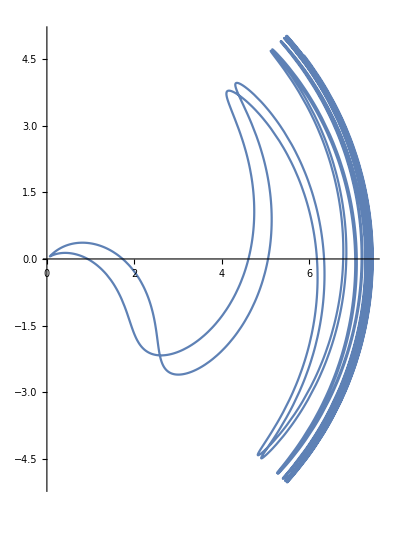

```mathematica
θ0 =π/2 
ΥZ = (π*Z2)/(2*EllipticK[KZ]);
qZ[λ_]:= ΥZ*λ 
z[λ_] :=Z1*JacobiSN[Z2*(λ + InverseJacobiCD[Cos[θ0]/Z1,KZ]/Z2 ) + EllipticK[KZ],KZ];
θ[λ_] := ArcCos[Z1*JacobiSN[Z2*(λ + InverseJacobiCD[Cos[θ0]/Z1,KZ]/Z2 ) + EllipticK[KZ],KZ]];
PolyZ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)


ParametricPlot[{r[λ]*Cos[π/2-θ[λ]],r[λ]*Sin[π/2-θ[λ]]} , {λ,-10,10}, PlotRange->All]
```

### Azimuthal Equation

```mathematica
Integrate[(a(ϵ(r^2+a^2)-a*L))/((r-RP)(r-RM))(1/(Sqrt[J](RI-r)^(3/2)(r-R4)^(1/2))), r]
```

-1/(-1. (-4.5+r) (-0.262398+r))^(3/2)1. (1.3391 (-4.5+r) (-0.262398+r)^2-(0.+0.490098 ⅈ) (-4.5+r)^(3/2) (-0.262398+r)^(3/2) Log[1.71414-1. r]-(0.+0.490098 ⅈ) (-4.5+r)^(3/2) (-0.262398+r)^(3/2) Log[-0.285857+1. r]+(0.+0.490098 ⅈ) (-4.5+r)^(3/2) (-0.262398+r)^(3/2) Log[5.80185-(0.+4.02212 ⅈ) √(-4.5+r) √(-0.262398+r)+1.33411 r]+(0.+0.490098 ⅈ) (-4.5+r)^(3/2) (-0.262398+r)^(3/2) Log[-1.00022-(0.+0.628837 ⅈ) √(-4.5+r) √(-0.262398+r)+4.19068 r])

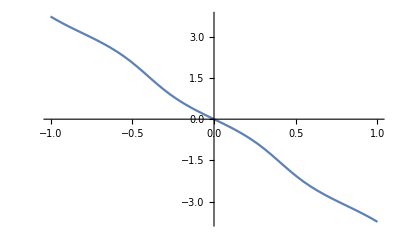

```mathematica
Υϕ =   L/EllipticK[KZ] EllipticPi[Z1^2, KZ];
qϕ[λ_] := Υϕ*λ + π/2;

Subscript[ϕ, r][λ_]:=1/(√J)2 a (((λ-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2))) (RI-R4)√J (-a L+a^2 ϵ+RI^2 ϵ))/(2(-R4+RI) (RI-RM) (RI-RP))+((-a L+a^2 ϵ+RM^2 ϵ) ArcTanh[(2  √(RM-R4))/((λ-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))  (RI-R4)√J √(RI-RM))])/(√(RM-R4) (RI-RM)^(3/2) (-RM+RP))+((-a L+a^2 ϵ+RP^2 ϵ) ArcTanh[(2  √(RP-R4))/((λ-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))  (RI-R4)√J √(RI-RP))])/(√(RP-R4) (RI-RP)^(3/2) (RM-RP)))  -1/(√J)2 a ((((-2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2))) (RI-R4)√J (-a L+a^2 ϵ+RI^2 ϵ))/(2(-R4+RI) (RI-RM) (RI-RP))+((-a L+a^2 ϵ+RM^2 ϵ) ArcTanh[(-2  √(RM-R4))/(((2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))  (RI-R4)√J √(RI-RM))])/(√(RM-R4) (RI-RM)^(3/2) (-RM+RP))+((-a L+a^2 ϵ+RP^2 ϵ) ArcTanh[(-2  √(RP-R4))/(((2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))  (RI-R4)√J √(RI-RP))])/(√(RP-R4) (RI-RP)^(3/2) (RM-RP)))  ;
Subscript[ϕ, θ][λ_] :=L/Z2 EllipticPi[Z1^2,JacobiAmplitude[Z2 (λ + InverseJacobiCD[Cos[θ0]/Z1,KZ]/Z2 )  + EllipticK[KZ],KZ],KZ]-L/Z2 EllipticPi[Z1^2,JacobiAmplitude[Z2 ( InverseJacobiCD[Cos[θ0]/Z1,KZ]/Z2 )  + EllipticK[KZ],KZ],KZ];

ϕ[λ_] := Subscript[ϕ, r][λ]+ Subscript[ϕ, θ][λ] -a*ϵ*λ

Plot[Subscript[ϕ, θ][λ],{λ,-1,1}]
```

```mathematica
Subscript[ϕ, θ][0]
```

-0.652271

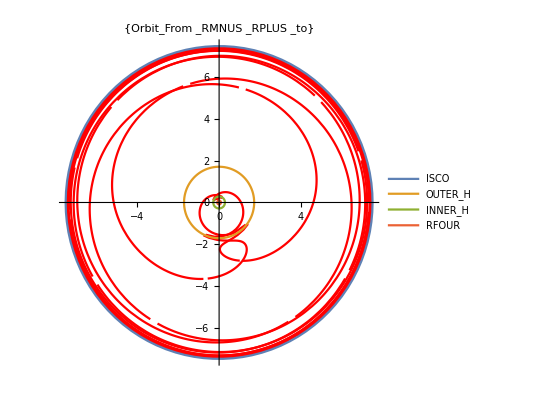

```mathematica
Q1 = ParametricPlot[{Re[r[λ]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Sin[Re[ϕ[λ]]]}, {λ,-10,10}, PlotRange->All, PlotLabel->{Orbit_From_RPLUS_to_RMNUS}, PlotStyle->Red, PlotLegends->ORBIT];
Q2 = ParametricPlot[{{RI*Cos[u],RI Sin[u]},{RP*Cos[u],RP Sin[u]},{RM*Cos[u],RM Sin[u]},{R4*Cos[u],R4 Sin[u]}},{u,-π,π},MaxRecursion->1,PlotRange->All,PlotLegends->{ISCO,OUTER_H,INNER_H,RFOUR}];

Show[Q1,Q2]
```

### 3D plots

### (*,Specularity[White,1000]*)

```mathematica
P1 = ParametricPlot3D[{Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]},{λ,-10,10}, PlotStyle->Red,PlotRange->All];
P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},MaxRecursion->4,PlotStyle->{Opacity[1],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
Show[P1,P2]
```

-Graphics3D-

### Time Function

#### Radial Part of time function

```mathematica
(*Clear[J,RI,R4,J,RM,RP]*)
```

```mathematica
Subscript[T, r][λ_]:= ((a^2+RI^2) (-a L+(a^2+RI^2) ϵ)(λ-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2))))/((RI-RM) (RI-RP))+(2 (R4-RI)^2 ϵ (λ-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2))))/(4+J (R4-RI)^2 (λ-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))^2)-(R4+3 RI+2 (RM+RP))/Sqrt[J] ϵ ArcTan[((λ-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))  (RI-R4)√J)/2]+(2 (a^2+RM^2) (-a L+a^2 ϵ+RM^2 ϵ) ArcTanh[(2  √(RM-R4))/((λ-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))  (RI-R4)√J √(RI-RM))])/(√(RM-R4) (RI-RM)^(3/2) (-RM+RP)Sqrt[J])+(2 (a^2+RP^2) (-a L+a^2 ϵ+RP^2 ϵ) ArcTanh[(2  √(RP-R4))/((λ-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))  (RI-R4)√J √(RI-RP))])/(Sqrt[J] √(RP-R4) (RI-RP)^(3/2) (RM-RP))-(((a^2+RI^2) (-a L+(a^2+RI^2) ϵ)((-2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2))))/((RI-RM) (RI-RP))+(2 (R4-RI)^2 ϵ ((-2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2))))/(4+J (R4-RI)^2 ((-2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))^2)-(R4+3 RI+2 (RM+RP))/Sqrt[J] ϵ ArcTan[(((-2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))  (RI-R4)√J)/2]+(2 (a^2+RM^2) (-a L+a^2 ϵ+RM^2 ϵ) ArcTanh[(-2  √(RM-R4))/(((2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))  (RI-R4)√J √(RI-RM))])/(√(RM-R4) (RI-RM)^(3/2) (-RM+RP)Sqrt[J])+(2 (a^2+RP^2) (-a L+a^2 ϵ+RP^2 ϵ) ArcTanh[(-2  √(RP-R4))/(((2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))  (RI-R4)√J √(RI-RP))])/(Sqrt[J] √(RP-R4) (RI-RP)^(3/2) (RM-RP)));


(*TPolyR[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)
Plot[{Subscript[T, r]'[λ],TPolyR[λ],Subscript[T, r]'[λ]-TPolyR[λ] },{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff}] - Must Change the branch we pick in negative time*)
```

#### ϕ part of time function

```mathematica
(*Clear["Global`*"]*)
```

```mathematica
(*tTildeϕ[ξ_] = -ϵ/(1-ϵ^2)Z2*EllipticE[ξ, KZ];*)

Subscript[T, z][λ_]:=1/J ϵ  (-Z2 EllipticE[JacobiAmplitude[Z2 (λ + InverseJacobiCD[Cos[θ0]/Z1,KZ]/Z2 ) + EllipticK[KZ],KZ],KZ]+(Z2-a^2 J/Z2) EllipticF[JacobiAmplitude[Z2 (λ + InverseJacobiCD[Cos[θ0]/Z1,KZ]/Z2 ) + EllipticK[KZ],KZ],KZ])-1/J ϵ  (-Z2 EllipticE[JacobiAmplitude[Z2 (InverseJacobiCD[Cos[θ0]/Z1,KZ]/Z2 ) + EllipticK[KZ],KZ],KZ]+(Z2-a^2 J/Z2) EllipticF[JacobiAmplitude[Z2 ( InverseJacobiCD[Cos[θ0]/Z1,KZ]/Z2 ) + EllipticK[KZ],KZ],KZ])
T[λ_]:= Subscript[T, r][λ]+Subscript[T, z][λ]+a*L*λ
```

### Mino Time in terms of Proper Time

```mathematica
Simplify[Integrate[r^2/(Sqrt[J](RI-r)^(3/2)(r-R4)^(1/2)), r]];
```

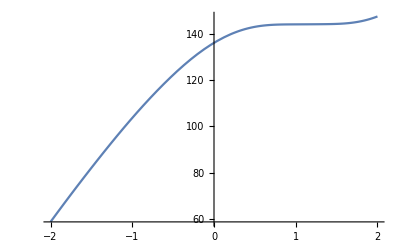

```mathematica
Subscript[τ, λr][λ_] :=(λ-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2))) (RI^2+(2(R4-RI)^2)/(4+J (R4-RI)^2(λ-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))^2))+((R4^2+2 R4 RI-3 RI^2) ArcTan[(λ-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))  (RI-R4)(√J)/2])/(√J (-R4+RI))-(-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2))) (RI^2+(2(R4-RI)^2)/(4+J (R4-RI)^2(-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))^2))+((R4^2+2 R4 RI-3 RI^2) ArcTan[(-(2 √(R0-R4))/(√(J (RI-R0) (R4-RI)^2)))  (RI-R4)(√J)/2])/(√J (-R4+RI))
Subscript[τ, λz][λ_] :=1/J Z2  (-EllipticE[ JacobiAmplitude[Z2 (λ + InverseJacobiCD[Cos[θ0]/Z1,KZ]/Z2 ) + EllipticK[KZ],KZ],KZ]+EllipticF[JacobiAmplitude[Z2 (λ + InverseJacobiCD[Cos[θ0]/Z1,KZ]/Z2 ) + EllipticK[KZ],KZ],KZ])-1/J Z2  (-EllipticE[ JacobiAmplitude[Z2 ( InverseJacobiCD[Cos[θ0]/Z1,KZ]/Z2 ) + EllipticK[KZ],KZ],KZ]+EllipticF[JacobiAmplitude[Z2 ( InverseJacobiCD[Cos[θ0]/Z1,KZ]/Z2 ) + EllipticK[KZ],KZ],KZ])


τ[λ_]:= Subscript[τ, λz][λ]+Subscript[τ, λr][λ]

Plot[τ[λ],{λ,-2,2}]
```

### Small Q approximation

```mathematica
RIQ[Q_] :=Sqrt[ (-4-a^2-Q+a^2 ϵ^2-√(12 a^2 Q (-3+3 ϵ^2)+(4+a^2+Q-a^2 ϵ^2)^2))/(6 (-1+ϵ^2))]
```

### Kruskal Coordinates

```mathematica
σP = (M*RP)/Sqrt[M^2-a^2];
σM = (M*RM)/Sqrt[M^2-a^2];
ν = σM/σP;


V[λ_] := Abs[r[λ]-RP]^(1/2)/Abs[r[λ]-RM]^(ν/2)Exp[(r[λ]+T[λ])/(2 σP)];
U[λ_] := -Abs[r[λ]-RP]^(1/2)/Abs[r[λ]-RM]^(ν/2)Exp[(r[λ]-T[λ])/(2 σP)];
ParametricPlot[{Re[U[λ]],Re[V[λ]]},{λ,-3,3}];
```

```mathematica
Integrate[1/Sqrt[(r-R1)(r-R2)(r-R3)(r-R4)], r];
```

### Analysis

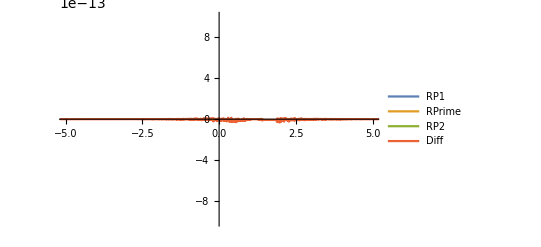

```mathematica
RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)

RPoly2[r_]:=J(RI-r)^3(r-R4)

Polyphir[r_]:= (a(ϵ(r^2+a^2)-a*L))/((r-RM)(r-RP));
Plot[{RPoly1[r[λ]], (r'[λ])^2, RPoly2[r[λ]], (r'[λ])^2- RPoly2[r[λ]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,RP2,Diff},  PlotRange->{{-5,5},{-0.0000000000010,0.0000000000010}}]
```

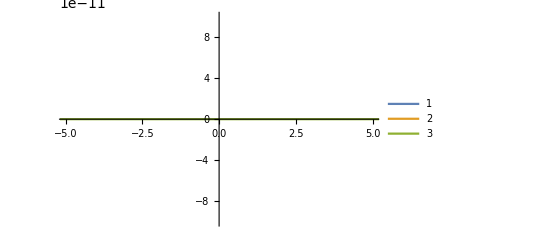

```mathematica
Polyθ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Plot[{(z'[λ])^2, Polyθ[λ], (z'[λ])^2- Polyθ[λ]}, {λ,-10,10}, PlotLegends->Automatic ,PlotLegends->{PolyθQ,θQ,θQ-PolyθQ}, PlotRange->{{-5,5},{-0.00000000010,0.00000000010}}]
```

```mathematica
|
```

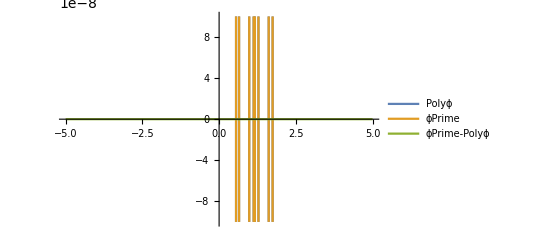

```mathematica
(*Plot[Im[ϕ[λ]],{λ,-5,5}]*)
Polyϕ[λ_]:= a/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L) + L/(1-z[λ]^2)-a*ϵ
Plot[{Polyϕ[λ],Re[ϕ'[λ]],Re[ϕ'[λ]-Polyϕ[λ]]},{λ,-5,5}, PlotRange->{{-5,5},{-0.00000010,0.00000010}},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ}]
```

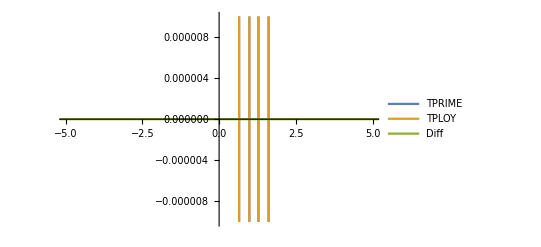

```mathematica
TPrime[λ_]:= Re[Piecewise[{{Subscript[T, r]'[λ]+Subscript[T, z]'[λ]+a*L,λ>0},{-Subscript[T, r]'[λ]+Subscript[T, z]'[λ]+a*L,λ<0}}]]
TPoly[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)-a^2 ϵ(1-z[λ]^2)+a*L
Plot[{Re[T'[λ]],TPoly[λ],Re[T'[λ]]-TPoly[λ] },{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff}, PlotRange->{{-5,5},{-0.000010,0.000010}}]
```

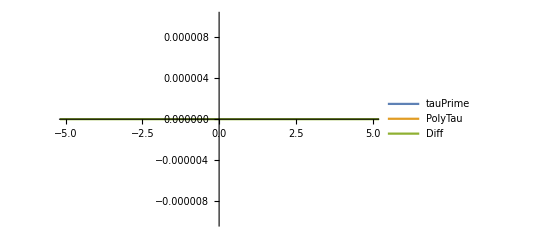

```mathematica
Plot[{τ'[λ],r[λ]^2+a^2 z[λ]^2,τ'[λ]-(r[λ]^2+a^2 z[λ]^2)},{λ,-10,20},{PlotLegends->{tauPrime,PolyTau,Diff}},PlotRange->{{-5,5},{-0.000010,0.000010}}]
```

```mathematica
FullSimplify[Together[((RI(RI-R4)^2 J*λ^2+4*R4)/((RI-R4)^2 J*λ^2+4)) (R4-RI)+RI (-R4+3 RI)]]
```

142.164+50.5862/(0.711684+1. λ^2)

```mathematica
Simplify[CoefficientList[(ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)-(1-ϵ^2)(RI-r)^3(r-(a^2 Q)/((1-ϵ^2)*RI^3)) ,r]]
```

{4.44089×10^-16,1.77636×10^-15,-2.66454×10^-15,1.77636×10^-15}

```mathematica
eq1 = 2 M Q-(3 a^2 Q)/RI+2 M (L-a ϵ)^2+RI^3 (-1+ϵ^2)==0
eq2 = -L^2-Q+3 RI^2-3 RI^2 ϵ^2+a^2 (-1+(3 Q)/RI^2+ϵ^2) == 0
eq3 = 2 M-(a^2 Q)/RI^3+3 RI (-1+ϵ^2)== 0
```

False

False

False

```mathematica
Solve[2 M-(a^2 Q)/RI^3+3 RI (-1+ϵ^2)== 0 ==0,ϵ]
```

Solve::ivar: 0.901278 is not a valid variable.

Solve[False,0.901278]

```mathematica
Solve[2 M Q-(3 a^2 Q)/RI+2 M (L-a ϵ)^2+RI^3 (-1+ϵ^2)==0,L]
```

Solve::ivar: 2.00432 is not a valid variable.

Solve[False,2.00432]

$Aborted